# 圆柱相交的交线和展开图

圆的参数方程

```mathematica
Manipulate[
ParametricPlot[{Cos[θ],Sin[θ]},{θ,-3.14,max},PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
{max,-Pi,Pi}
]
```

圆柱的参数方程

```mathematica
ParametricPlot3D[{Cos[θ],Sin[θ],h},{θ,-Pi,Pi},{h,-2,2},PlotTheme->"Classic"]
```

-Graphics3D-

两圆柱垂直相交，画出交线。mesh参数指定了meshFunctions值为0时画分割线，所以meshFunction是两个函数相减的形式：由于两圆柱的方程写作x^2 + y^2 == h, x^2 + z^2 ==h 相减后为y^2-z^2，所以#2^2-#3^2

```mathematica
ParametricPlot3D[{{Cos[θ],Sin[θ],h},{Cos[θ],h,Sin[θ]}},{θ,-Pi,Pi},{h,-2,2},MeshFunctions->{#2^2-#3^2&},Mesh->{{{0,Directive[Thick,Red]}}},PlotStyle->{Opacity[0.5],Opacity[1]},PlotTheme->"Classic"]
```

-Graphics3D-

ContourPlot形式，先绘制一个同心圆

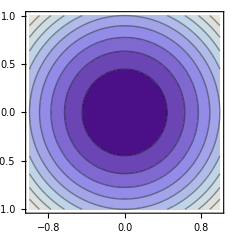

```mathematica
ContourPlot[{x^2+y^2},{x,-1,1},{y,-1,1},PlotTheme->"Classic"]
```

当x^2+y^2==1时上图的同心圆会收缩成一个半径为1的圆，圆柱同理

```mathematica
ContourPlot3D[{{x^2+y^2==1},{x^2+z^2==1}},{x,-2,2},{y,-2,2},{z,-2,2},MeshFunctions->{#2^2-#3^2&},Mesh->{{{0,Directive[Thick,Red]}}},PlotTheme->"Classic"]
```

-Graphics3D-

## RegionPlot3D

绘制三维区域：两圆柱相交区域

```mathematica
RegionPlot3D[{{x^2+y^2<=1 && x^2+z^2<= 1}},{x,-1,1},{y,-1,1},{z,-1,1},PlotPoints->100,PlotTheme->"Classic"]
```

-Graphics3D-